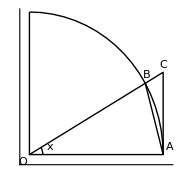

```mathematica
Graphics[{Circle[{0,0},1,{0,Pi/2}],Circle[{0,0},0.1,{0,x}],Line[{{0,1},{0,0},{1,0},{1,Tan[x]},{0,0}}],Line[{{1,0},{Cos[x],Sin[x]}}],Inset["x",{0.15,0.05}],Inset["O",{-0.05,-0.05}],Inset["A",{1.05,0.05}],Inset["B",{Cos[x]+0.01,Sin[x]+0.06}],Inset["C",{1,Tan[x]+0.05}]},ImageSize->Small,Axes->True,Ticks->None]/.{x->Pi/6}
```

```mathematica
证明 (sin x)/xx0=1.
证明：令 f(x)=((sin x)/x). 这个函数除了 x=0 之外处处有定义. 显然，对任何 x≠0，有f(-x)=f(x).
```

```mathematica
首先证明 f(0+)=1. 考察区间 (0,π/2)，作中心在原点、半径为 1 的圆周（单位圆）在第一象限那一部分中的圆弧. 过圆心作角度为 x 的射线，与圆弧相交于点 B，过点 A 作与横轴的垂线与 OB 延长线交于点 C.  由图中可以看出 ΔAOB 的面积<扇形 ABO 的面积<ΔAOC 的面积. 由于 x∈(0,π/2)，以上关系可以推出以下的不等式.
```

```mathematica
sin x<x<tan x
```

```mathematica
由此推出
```

```mathematica
cos x<(sin x)/x<1
```

```mathematica
进一步得到
```

```mathematica
0<1-(sin x)/x<1-cos x=2 sin^2 x/2<x^2/2<π/4 x
```

```mathematica
因此，∀ϵ>0，取 δ=min(π/2,(4ϵ)/π)，当 0<x<δ 时
```

```mathematica
0<1-(sin x)/x<π/4 x<π/4 δ≤ϵ
```

```mathematica
依定义可知 f(0+)=1. 由于 f 是一个偶函数，也有 f(0-)=1. 所以 f(0+)=f(0-)=1，由此可知
```

```mathematica
lim_(x->0) (sin x)/x=1
```

```mathematica
求 ln|x| 的导数
```

```mathematica
解：当 x>0时
```

```mathematica
ⅆ/ⅆx ln x=lim_(Δx->0) (ln(x+Δx)-ln(x))/Δx=lim_(Δx->0) (ln(1+Δx/x))^(x/Δx 1/x)=1/x lim_(Δx->0) (ln(1+Δx/x))^(x/Δx)
```

```mathematica
当 Δx->0时，x/Δx->∞，(1+Δx/x)^(x/Δx)->e，因此
```

```mathematica
d/ⅆx ln x=1/x ln ⅇ=1/x
```

```mathematica
当 x<0时
```

```mathematica
ⅆ/ⅆx ln|x|=ⅆ/ⅆx ln(-x)=-ⅆ/(ⅆ(-x))ln(-x)=1/x
```

```mathematica
求 Subscript[log, a]|x| 的导数
解：
```

```mathematica
ⅆ/ⅆx Subscript[log, a]|x|=ⅆ/ⅆx(ln |x|)/(ln a)=1/(x ln a)
```

```mathematica
求 ⅇ^x 的导数
```

```mathematica
解：令 y=e^x，利用反函数求导规则
```

```mathematica
ⅆ/ⅆx ⅇ^x=ⅆy/(ⅆln y)=y=e^x
```

```mathematica
求 a^x 的导数
解：
```

```mathematica
ⅆ/ⅆx a^x=ⅆ/ⅆx e^(x ln a)=a^x ln a
```

```mathematica
求 x^x 的导数
解：
```

```mathematica
ⅆ/ⅆx x^x=ⅆ/ⅆx ⅇ^(x ln x)=x^x(1+ln x)
```

```mathematica
求 sin^-1 x 的导数
解：令 y=sin^-1 x，则 x=sin y，其中 x∈(-1,1)，y∈(-π/2,π/2). 利用反函数求导规则
```

```mathematica
(ⅆ sin^-1 x)/ⅆx=ⅆy/(ⅆsin y)=1/(cos y)=1/(√(1-sin^2 y))=1/(√(1-x^2))
```

```mathematica
这里当 y∈(-π/2,π/2)时，cos y≥0，所以根式应取正值.
```